# Homework 4

```mathematica
Needs["VariationalMethods`"]
```

### Question 1

```mathematica
ClearAll[w0];
γ = 1/10;
ham[u_,v_,w_] = -(1/4)*v^4 +( 1/2)*(w - u^2 + γ)*v^2 - (1/4)*u^4 + (1/2)*w*u^2 -w*u+u-(3/4)+(1/2)w;
```

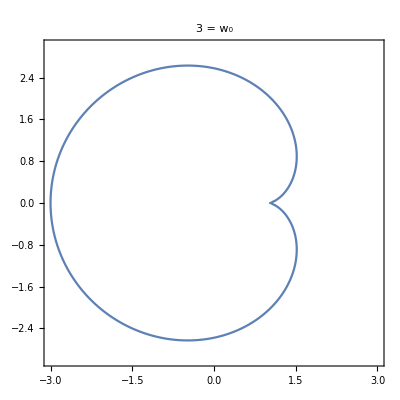

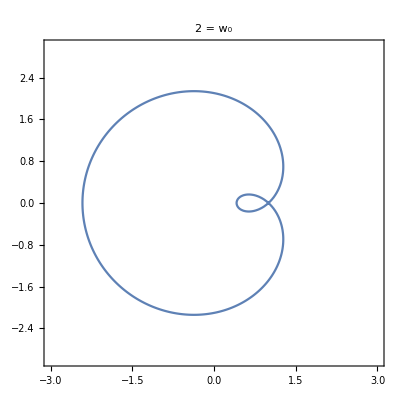

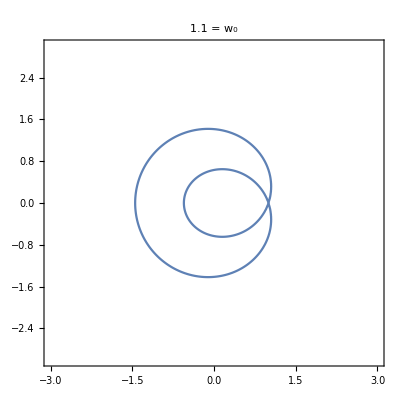

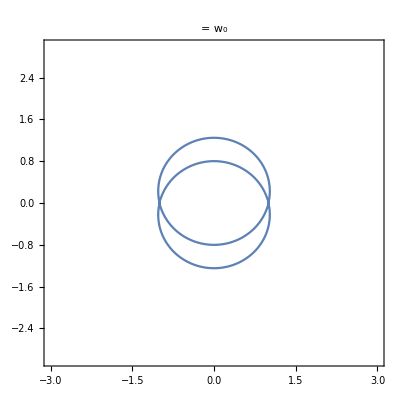

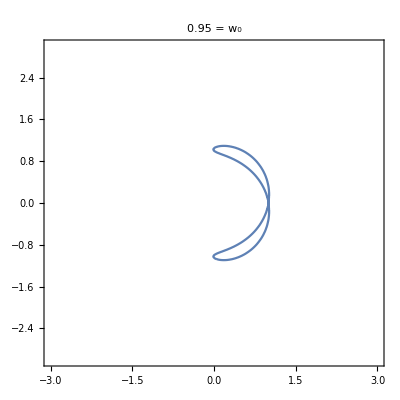

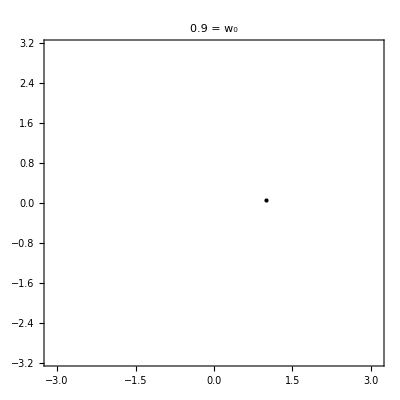

```mathematica
w0 = {3,2,1.1,1,0.95,0.9};
For[i=1,i<7,i++,ContourPlot[ham[u,v,w0[[i]]]==0,{u,-3,3},{v,-3,3}, PlotLabel->"= w_0"w0[[i]],PlotPoints->100]//Print]
```

### Question 4

Define Conserved Quantities

```mathematica
Fmin1[x_] = u;
F0[x_] = (1/2) *u[x]^2;
F1[x_] = (1/6)*u[x]^3 - (1/2)*D[u[x],x]^2;
F2[x_] = (1/24 )* u[x]^4 - (1/2)*u[x]*D[u[x],x]^2+(3/10)*D[u[x],{x,2}]^2;
```

Notice that {F_i,F_-1} = 0 for all i

```mathematica
D[VariationalD[Fmin1[x],u[x],x],x]
```

0

Check F0 and F1

```mathematica
VariationalD[VariationalD[F0[x],u[x],x]*D[VariationalD[F1[x],u[x],x],x],u[x],x]
```

0

Check F0 and F2

```mathematica
VariationalD[VariationalD[F0[x],u[x],x]*D[VariationalD[F2[x],u[x],x],x],u[x],x]
```

0

Check F1 and F 2

```mathematica
VariationalD[VariationalD[F1[x],u[x],x]*D[VariationalD[F2[x],u[x],x],x],u[x],x]
```

0

### Question 5

```mathematica
ClearAll[a1,a2,c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12]
```

```mathematica
ut[x_,t_] =u[x,t]*D[u[x,t],x] + D[u[x,t],{x,3}];
```

```mathematica
ft[x_,t_] = 1/6 * u[x,t]^3 * ut[x,t]+a1*2*u[x,t]*D[u[x,t],x]*D[ut[x,t],x] + a1*ut[x,t]*D[u[x,t],x]^2 + a2*2*D[u[x,t],{x,2}]*D[ut[x,t],{x,2}];
```

```mathematica
g [x_,t_]= c1*u[x,t]^5+c2*u[x,t]^3*D[u[x,t],{x,2}] +c3*u[x,t]^2*D[u[x,t],x]^2 + c4*u[x,t]^2*D[u[x,t],{x,4}] + c5 * u[x,t]*D[u[x,t],x]*D[u[x,t],{x,3}] + c6*u[x,t]*D[u[x,t],{x,2}]^2 +c7*D[u[x,t],x]^2*D[u[x,t],{x,2}] + c8*u[x,t]*D[u[x,t],{x,6}] + c9*D[u[x,t],x]*D[u[x,t],{x,5}] + c10 *D[u[x,t],{x,2}]*D[u[x,t],{x,4}] + c11*D[u[x,t],{x,3}]^2 + c12*D[u[x,t],{x,8}];
```

```mathematica
gx[x_,t_] = D[g[x,t],x];
```

```mathematica
result[x,t] = ft[x,t]+gx[x,t];
```

```mathematica
FullSimplify[result[x,t]]
```

1/6 (-1+30 c1) u[x,t]^4 u^(1,0)[x,t]+1/6 (-1+6 c2) u[x,t]^3 u^(3,0)[x,t]+(-a1+c5+c7) (u^(1,0)[x,t])^2 u^(3,0)[x,t]+(c10+2 c11) u^(3,0)[x,t] u^(4,0)[x,t]+(-2 a2+c10+c9) u^(2,0)[x,t] u^(5,0)[x,t]+u[x,t]^2 ((-2 a1+3 c2+2 c3) u^(1,0)[x,t] u^(2,0)[x,t]+c4 u^(5,0)[x,t])+u^(1,0)[x,t] ((-6 a2+c6+2 c7) (u^(2,0)[x,t])^2+(c8+c9) u^(6,0)[x,t])+u[x,t] ((-3 a1+2 c3) (u^(1,0)[x,t])^3+(-2 a2+c5+2 c6) u^(2,0)[x,t] u^(3,0)[x,t]+(-2 a1+2 c4+c5) u^(1,0)[x,t] u^(4,0)[x,t]+c8 u^(7,0)[x,t])+c12 u^(9,0)[x,t]

### Question 7

Verifying that U is a solution

```mathematica
U[x_] = 2 * D[Log[1 + Exp[k*x+α]],{x,2}]
```

2 (-(ⅇ^(2 k x+2 α) k^2)/((1+ⅇ^(k x+α))^2)+(ⅇ^(k x+α) k^2)/(1+ⅇ^(k x+α)))

```mathematica
Simplify[6*U[x]*D[U[x],x]+D[U[x],{x,3}]+ Subscript[c, 0]*D[U[x],x]]
```

-(2 ⅇ^(k x+α) (-1+ⅇ^(k x+α)) k^3 (k^2+c_0))/((1+ⅇ^(k x+α))^3)

Consider KdV1

```mathematica
u[x_,t1_,t2_,t3_] = 2 * D[Log[1 + Exp[k*x+α[t1,t2,t3]]],{x,2}]
```

2 (-(ⅇ^(2 k x+2 α[t1,t2,t3]) k^2)/((1+ⅇ^(k x+α[t1,t2,t3]))^2)+(ⅇ^(k x+α[t1,t2,t3]) k^2)/(1+ⅇ^(k x+α[t1,t2,t3])))

```mathematica
KdV1[x_,t1_,t2_,t3_]=-D[u[x,t1,t2,t3],t1]+6*u[x,t1,t2,t3]*D[u[x,t1,t2,t3],x]+D[u[x,t1,t2,t3],{x,3}];
```

```mathematica
FullSimplify[KdV1[x,t1,t2,t3]]
```

4 k^2 Csch[k x+α[t1,t2,t3]]^3 Sinh[1/2 (k x+α[t1,t2,t3])]^4 (-k^3+α^(1,0,0)[t1,t2,t3])

Consider KdV2

```mathematica
KdV2[x_,t1_,t2_,t3_] =-D[u[x,t1,t2,t3],t2]+30*u[x,t1,t2,t3]^2*D[u[x,t1,t2,t3],x] + 20*D[u[x,t1,t2,t3],x]*D[u[x,t1,t2,t3],{x,2}] + 10*u[x,t1,t2,t3]*D[u[x,t1,t2,t3],{x,3}]+D[u[x,t1,t2,t3],{x,5}];
```

```mathematica
FullSimplify[KdV2[x,t1,t2,t3]]
```

4 k^2 Csch[k x+α[t1,t2,t3]]^3 Sinh[1/2 (k x+α[t1,t2,t3])]^4 (-k^5+α^(0,1,0)[t1,t2,t3])

Consider KdV3

```mathematica
KdV3[x_,t1_,t2_,t3_] =-D[u[x,t1,t2,t3],t3] +140*u[x,t1,t2,t3]^3*D[u[x,t1,t2,t3],x] + 70 * D[u[x,t1,t2,t3],x]^3 + 280*u[x,t1,t2,t3]*D[u[x,t1,t2,t3],x]*D[u[x,t1,t2,t3],{x,2}] + 70*D[u[x,t1,t2,t3],{x,2}]*D[u[x,t1,t2,t3],{x,3}]+70*u[x,t1,t2,t3]^2*D[u[x,t1,t2,t3],{x,3}]+42*D[u[x,t1,t2,t3],x]*D[u[x,t1,t2,t3],{x,4}]+14*u[x,t1,t2,t3]*D[u[x,t1,t2,t3],{x,5}]+D[u[x,t1,t2,t3],{x,7}];
```

```mathematica
FullSimplify[KdV3[x,t1,t2,t3]]
```

4 k^2 Csch[k x+α[t1,t2,t3]]^3 Sinh[1/2 (k x+α[t1,t2,t3])]^4 (-k^7+α^(0,0,1)[t1,t2,t3])

### Question 8

```mathematica
U[x_]=2*D[Log[1 + Exp[k1*x+α]+Exp[k2*x +β]+Power[(k1-k2)/(k1+k2),2]*Exp[k1*x+k2*x+α+β]],{x,2}];
```

First use Together to get a common den between all terms. Then look at when the num is zero and get rid of extra stuff

```mathematica
gross[x_] = 30*U[x]^2*D[U[x],x]+ 20*D[U[x],x]*D[U[x],{x,2}]+10*U[x]*D[U[x],{x,3}]+D[U[x],{x,5}]+c1*(6*U[x]*D[U[x],x] + D[U[x],{x,3}])+c0*D[U[x],x];
shortGross = Numerator[Together[gross[x]]] / (2(k1+k2)^2)
```

c0 ⅇ^(k1 x+α) k1^7-c0 ⅇ^(2 k1 x+2 α) k1^7+3 c0 ⅇ^(k1 x+k2 x+α+β) k1^7-3 c0 ⅇ^(2 k1 x+k2 x+2 α+β) k1^7+3 c0 ⅇ^(k1 x+2 k2 x+α+2 β) k1^7-3 c0 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1^7+c0 ⅇ^(k1 x+3 k2 x+α+3 β) k1^7-c0 ⅇ^(2 k1 x+3 k2 x+2 α+3 β) k1^7+c1 ⅇ^(k1 x+α) k1^9-c1 ⅇ^(2 k1 x+2 α) k1^9+3 c1 ⅇ^(k1 x+k2 x+α+β) k1^9-3 c1 ⅇ^(2 k1 x+k2 x+2 α+β) k1^9+3 c1 ⅇ^(k1 x+2 k2 x+α+2 β) k1^9-3 c1 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1^9+c1 ⅇ^(k1 x+3 k2 x+α+3 β) k1^9-c1 ⅇ^(2 k1 x+3 k2 x+2 α+3 β) k1^9+ⅇ^(k1 x+α) k1^11-ⅇ^(2 k1 x+2 α) k1^11+3 ⅇ^(k1 x+k2 x+α+β) k1^11-3 ⅇ^(2 k1 x+k2 x+2 α+β) k1^11+3 ⅇ^(k1 x+2 k2 x+α+2 β) k1^11-3 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1^11+ⅇ^(k1 x+3 k2 x+α+3 β) k1^11-ⅇ^(2 k1 x+3 k2 x+2 α+3 β) k1^11+4 c0 ⅇ^(k1 x+α) k1^6 k2-4 c0 ⅇ^(2 k1 x+2 α) k1^6 k2+8 c0 ⅇ^(k1 x+k2 x+α+β) k1^6 k2-4 c0 ⅇ^(2 k1 x+k2 x+2 α+β) k1^6 k2+4 c0 ⅇ^(k1 x+2 k2 x+α+2 β) k1^6 k2+4 c0 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1^6 k2+4 c0 ⅇ^(2 k1 x+3 k2 x+2 α+3 β) k1^6 k2+4 c1 ⅇ^(k1 x+α) k1^8 k2-4 c1 ⅇ^(2 k1 x+2 α) k1^8 k2+8 c1 ⅇ^(k1 x+k2 x+α+β) k1^8 k2-4 c1 ⅇ^(2 k1 x+k2 x+2 α+β) k1^8 k2+4 c1 ⅇ^(k1 x+2 k2 x+α+2 β) k1^8 k2+4 c1 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1^8 k2+4 c1 ⅇ^(2 k1 x+3 k2 x+2 α+3 β) k1^8 k2+4 ⅇ^(k1 x+α) k1^10 k2-4 ⅇ^(2 k1 x+2 α) k1^10 k2+8 ⅇ^(k1 x+k2 x+α+β) k1^10 k2-4 ⅇ^(2 k1 x+k2 x+2 α+β) k1^10 k2+4 ⅇ^(k1 x+2 k2 x+α+2 β) k1^10 k2+4 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1^10 k2+4 ⅇ^(2 k1 x+3 k2 x+2 α+3 β) k1^10 k2+6 c0 ⅇ^(k1 x+α) k1^5 k2^2-6 c0 ⅇ^(2 k1 x+2 α) k1^5 k2^2-2 c0 ⅇ^(k1 x+k2 x+α+β) k1^5 k2^2+10 c0 ⅇ^(2 k1 x+k2 x+2 α+β) k1^5 k2^2-10 c0 ⅇ^(k1 x+2 k2 x+α+2 β) k1^5 k2^2+10 c0 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1^5 k2^2-2 c0 ⅇ^(k1 x+3 k2 x+α+3 β) k1^5 k2^2-6 c0 ⅇ^(2 k1 x+3 k2 x+2 α+3 β) k1^5 k2^2+6 c1 ⅇ^(k1 x+α) k1^7 k2^2-6 c1 ⅇ^(2 k1 x+2 α) k1^7 k2^2+2 c1 ⅇ^(k1 x+k2 x+α+β) k1^7 k2^2+6 c1 ⅇ^(2 k1 x+k2 x+2 α+β) k1^7 k2^2-6 c1 ⅇ^(k1 x+2 k2 x+α+2 β) k1^7 k2^2+6 c1 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1^7 k2^2-2 c1 ⅇ^(k1 x+3 k2 x+α+3 β) k1^7 k2^2-6 c1 ⅇ^(2 k1 x+3 k2 x+2 α+3 β) k1^7 k2^2+6 ⅇ^(k1 x+α) k1^9 k2^2-6 ⅇ^(2 k1 x+2 α) k1^9 k2^2+2 ⅇ^(k1 x+k2 x+α+β) k1^9 k2^2+6 ⅇ^(2 k1 x+k2 x+2 α+β) k1^9 k2^2-6 ⅇ^(k1 x+2 k2 x+α+2 β) k1^9 k2^2+6 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1^9 k2^2-2 ⅇ^(k1 x+3 k2 x+α+3 β) k1^9 k2^2-6 ⅇ^(2 k1 x+3 k2 x+2 α+3 β) k1^9 k2^2+4 c0 ⅇ^(k1 x+α) k1^4 k2^3-4 c0 ⅇ^(2 k1 x+2 α) k1^4 k2^3+c0 ⅇ^(k2 x+β) k1^4 k2^3-25 c0 ⅇ^(k1 x+k2 x+α+β) k1^4 k2^3+11 c0 ⅇ^(2 k1 x+k2 x+2 α+β) k1^4 k2^3+c0 ⅇ^(3 k1 x+k2 x+3 α+β) k1^4 k2^3-c0 ⅇ^(2 k2 x+2 β) k1^4 k2^3-11 c0 ⅇ^(k1 x+2 k2 x+α+2 β) k1^4 k2^3-11 c0 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1^4 k2^3-c0 ⅇ^(3 k1 x+2 k2 x+3 α+2 β) k1^4 k2^3+4 c0 ⅇ^(2 k1 x+3 k2 x+2 α+3 β) k1^4 k2^3+4 c1 ⅇ^(k1 x+α) k1^6 k2^3-4 c1 ⅇ^(2 k1 x+2 α) k1^6 k2^3-12 c1 ⅇ^(k1 x+k2 x+α+β) k1^6 k2^3+8 c1 ⅇ^(2 k1 x+k2 x+2 α+β) k1^6 k2^3-8 c1 ⅇ^(k1 x+2 k2 x+α+2 β) k1^6 k2^3-8 c1 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1^6 k2^3+4 c1 ⅇ^(2 k1 x+3 k2 x+2 α+3 β) k1^6 k2^3+4 ⅇ^(k1 x+α) k1^8 k2^3-4 ⅇ^(2 k1 x+2 α) k1^8 k2^3-12 ⅇ^(k1 x+k2 x+α+β) k1^8 k2^3+8 ⅇ^(2 k1 x+k2 x+2 α+β) k1^8 k2^3-8 ⅇ^(k1 x+2 k2 x+α+2 β) k1^8 k2^3-8 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1^8 k2^3+4 ⅇ^(2 k1 x+3 k2 x+2 α+3 β) k1^8 k2^3+c0 ⅇ^(k1 x+α) k1^3 k2^4-c0 ⅇ^(2 k1 x+2 α) k1^3 k2^4+4 c0 ⅇ^(k2 x+β) k1^3 k2^4-25 c0 ⅇ^(k1 x+k2 x+α+β) k1^3 k2^4-11 c0 ⅇ^(2 k1 x+k2 x+2 α+β) k1^3 k2^4-4 c0 ⅇ^(2 k2 x+2 β) k1^3 k2^4+11 c0 ⅇ^(k1 x+2 k2 x+α+2 β) k1^3 k2^4-11 c0 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1^3 k2^4+4 c0 ⅇ^(3 k1 x+2 k2 x+3 α+2 β) k1^3 k2^4+c0 ⅇ^(k1 x+3 k2 x+α+3 β) k1^3 k2^4-c0 ⅇ^(2 k1 x+3 k2 x+2 α+3 β) k1^3 k2^4+c1 ⅇ^(k1 x+α) k1^5 k2^4-c1 ⅇ^(2 k1 x+2 α) k1^5 k2^4-17 c1 ⅇ^(k1 x+k2 x+α+β) k1^5 k2^4+c1 ⅇ^(2 k1 x+k2 x+2 α+β) k1^5 k2^4-c1 ⅇ^(k1 x+2 k2 x+α+2 β) k1^5 k2^4+c1 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1^5 k2^4+c1 ⅇ^(k1 x+3 k2 x+α+3 β) k1^5 k2^4-c1 ⅇ^(2 k1 x+3 k2 x+2 α+3 β) k1^5 k2^4+ⅇ^(k1 x+α) k1^7 k2^4-ⅇ^(2 k1 x+2 α) k1^7 k2^4-13 ⅇ^(k1 x+k2 x+α+β) k1^7 k2^4-3 ⅇ^(2 k1 x+k2 x+2 α+β) k1^7 k2^4+3 ⅇ^(k1 x+2 k2 x+α+2 β) k1^7 k2^4-3 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1^7 k2^4+ⅇ^(k1 x+3 k2 x+α+3 β) k1^7 k2^4-ⅇ^(2 k1 x+3 k2 x+2 α+3 β) k1^7 k2^4+6 c0 ⅇ^(k2 x+β) k1^2 k2^5-2 c0 ⅇ^(k1 x+k2 x+α+β) k1^2 k2^5-10 c0 ⅇ^(2 k1 x+k2 x+2 α+β) k1^2 k2^5-2 c0 ⅇ^(3 k1 x+k2 x+3 α+β) k1^2 k2^5-6 c0 ⅇ^(2 k2 x+2 β) k1^2 k2^5+10 c0 ⅇ^(k1 x+2 k2 x+α+2 β) k1^2 k2^5+10 c0 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1^2 k2^5-6 c0 ⅇ^(3 k1 x+2 k2 x+3 α+2 β) k1^2 k2^5+c1 ⅇ^(k2 x+β) k1^4 k2^5-17 c1 ⅇ^(k1 x+k2 x+α+β) k1^4 k2^5-c1 ⅇ^(2 k1 x+k2 x+2 α+β) k1^4 k2^5+c1 ⅇ^(3 k1 x+k2 x+3 α+β) k1^4 k2^5-c1 ⅇ^(2 k2 x+2 β) k1^4 k2^5+c1 ⅇ^(k1 x+2 k2 x+α+2 β) k1^4 k2^5+c1 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1^4 k2^5-c1 ⅇ^(3 k1 x+2 k2 x+3 α+2 β) k1^4 k2^5-4 ⅇ^(k1 x+k2 x+α+β) k1^6 k2^5-4 ⅇ^(2 k1 x+k2 x+2 α+β) k1^6 k2^5+4 ⅇ^(k1 x+2 k2 x+α+2 β) k1^6 k2^5+4 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1^6 k2^5+4 c0 ⅇ^(k2 x+β) k1 k2^6+8 c0 ⅇ^(k1 x+k2 x+α+β) k1 k2^6+4 c0 ⅇ^(2 k1 x+k2 x+2 α+β) k1 k2^6-4 c0 ⅇ^(2 k2 x+2 β) k1 k2^6-4 c0 ⅇ^(k1 x+2 k2 x+α+2 β) k1 k2^6+4 c0 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1 k2^6+4 c0 ⅇ^(3 k1 x+2 k2 x+3 α+2 β) k1 k2^6+4 c1 ⅇ^(k2 x+β) k1^3 k2^6-12 c1 ⅇ^(k1 x+k2 x+α+β) k1^3 k2^6-8 c1 ⅇ^(2 k1 x+k2 x+2 α+β) k1^3 k2^6-4 c1 ⅇ^(2 k2 x+2 β) k1^3 k2^6+8 c1 ⅇ^(k1 x+2 k2 x+α+2 β) k1^3 k2^6-8 c1 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1^3 k2^6+4 c1 ⅇ^(3 k1 x+2 k2 x+3 α+2 β) k1^3 k2^6-4 ⅇ^(k1 x+k2 x+α+β) k1^5 k2^6+4 ⅇ^(2 k1 x+k2 x+2 α+β) k1^5 k2^6-4 ⅇ^(k1 x+2 k2 x+α+2 β) k1^5 k2^6+4 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1^5 k2^6+c0 ⅇ^(k2 x+β) k2^7+3 c0 ⅇ^(k1 x+k2 x+α+β) k2^7+3 c0 ⅇ^(2 k1 x+k2 x+2 α+β) k2^7+c0 ⅇ^(3 k1 x+k2 x+3 α+β) k2^7-c0 ⅇ^(2 k2 x+2 β) k2^7-3 c0 ⅇ^(k1 x+2 k2 x+α+2 β) k2^7-3 c0 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k2^7-c0 ⅇ^(3 k1 x+2 k2 x+3 α+2 β) k2^7+6 c1 ⅇ^(k2 x+β) k1^2 k2^7+2 c1 ⅇ^(k1 x+k2 x+α+β) k1^2 k2^7-6 c1 ⅇ^(2 k1 x+k2 x+2 α+β) k1^2 k2^7-2 c1 ⅇ^(3 k1 x+k2 x+3 α+β) k1^2 k2^7-6 c1 ⅇ^(2 k2 x+2 β) k1^2 k2^7+6 c1 ⅇ^(k1 x+2 k2 x+α+2 β) k1^2 k2^7+6 c1 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1^2 k2^7-6 c1 ⅇ^(3 k1 x+2 k2 x+3 α+2 β) k1^2 k2^7+ⅇ^(k2 x+β) k1^4 k2^7-13 ⅇ^(k1 x+k2 x+α+β) k1^4 k2^7+3 ⅇ^(2 k1 x+k2 x+2 α+β) k1^4 k2^7+ⅇ^(3 k1 x+k2 x+3 α+β) k1^4 k2^7-ⅇ^(2 k2 x+2 β) k1^4 k2^7-3 ⅇ^(k1 x+2 k2 x+α+2 β) k1^4 k2^7-3 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1^4 k2^7-ⅇ^(3 k1 x+2 k2 x+3 α+2 β) k1^4 k2^7+4 c1 ⅇ^(k2 x+β) k1 k2^8+8 c1 ⅇ^(k1 x+k2 x+α+β) k1 k2^8+4 c1 ⅇ^(2 k1 x+k2 x+2 α+β) k1 k2^8-4 c1 ⅇ^(2 k2 x+2 β) k1 k2^8-4 c1 ⅇ^(k1 x+2 k2 x+α+2 β) k1 k2^8+4 c1 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1 k2^8+4 c1 ⅇ^(3 k1 x+2 k2 x+3 α+2 β) k1 k2^8+4 ⅇ^(k2 x+β) k1^3 k2^8-12 ⅇ^(k1 x+k2 x+α+β) k1^3 k2^8-8 ⅇ^(2 k1 x+k2 x+2 α+β) k1^3 k2^8-4 ⅇ^(2 k2 x+2 β) k1^3 k2^8+8 ⅇ^(k1 x+2 k2 x+α+2 β) k1^3 k2^8-8 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1^3 k2^8+4 ⅇ^(3 k1 x+2 k2 x+3 α+2 β) k1^3 k2^8+c1 ⅇ^(k2 x+β) k2^9+3 c1 ⅇ^(k1 x+k2 x+α+β) k2^9+3 c1 ⅇ^(2 k1 x+k2 x+2 α+β) k2^9+c1 ⅇ^(3 k1 x+k2 x+3 α+β) k2^9-c1 ⅇ^(2 k2 x+2 β) k2^9-3 c1 ⅇ^(k1 x+2 k2 x+α+2 β) k2^9-3 c1 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k2^9-c1 ⅇ^(3 k1 x+2 k2 x+3 α+2 β) k2^9+6 ⅇ^(k2 x+β) k1^2 k2^9+2 ⅇ^(k1 x+k2 x+α+β) k1^2 k2^9-6 ⅇ^(2 k1 x+k2 x+2 α+β) k1^2 k2^9-2 ⅇ^(3 k1 x+k2 x+3 α+β) k1^2 k2^9-6 ⅇ^(2 k2 x+2 β) k1^2 k2^9+6 ⅇ^(k1 x+2 k2 x+α+2 β) k1^2 k2^9+6 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1^2 k2^9-6 ⅇ^(3 k1 x+2 k2 x+3 α+2 β) k1^2 k2^9+4 ⅇ^(k2 x+β) k1 k2^10+8 ⅇ^(k1 x+k2 x+α+β) k1 k2^10+4 ⅇ^(2 k1 x+k2 x+2 α+β) k1 k2^10-4 ⅇ^(2 k2 x+2 β) k1 k2^10-4 ⅇ^(k1 x+2 k2 x+α+2 β) k1 k2^10+4 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k1 k2^10+4 ⅇ^(3 k1 x+2 k2 x+3 α+2 β) k1 k2^10+ⅇ^(k2 x+β) k2^11+3 ⅇ^(k1 x+k2 x+α+β) k2^11+3 ⅇ^(2 k1 x+k2 x+2 α+β) k2^11+ⅇ^(3 k1 x+k2 x+3 α+β) k2^11-ⅇ^(2 k2 x+2 β) k2^11-3 ⅇ^(k1 x+2 k2 x+α+2 β) k2^11-3 ⅇ^(2 k1 x+2 k2 x+2 α+2 β) k2^11-ⅇ^(3 k1 x+2 k2 x+3 α+2 β) k2^11

Get two random terms

```mathematica
coef1 = Coefficient[shortGross,ⅇ^(k1 x+2 k2 x+α+2 β)];
coef2 = Coefficient[shortGross,ⅇ^(2 k1 x+2 k2 x+2 α+2 β)];
```

Solve the 2x2 system and hope for the best

```mathematica
Solve[{coef1==0,coef2==0},{c0,c1}]
```

{{c0→k1^2 k2^2,c1→-k1^2-k2^2}}

Let’s double check these values (Yay!)

```mathematica
c0 = k1^2*k2^2;
c1 = -k1^2 - k2^2;
Simplify[shortGross]
```

0

```mathematica
ClearAll[c0,c1,k1,k2]
u[x_,t1_,t2_,t3_]=2*D[Log[1 + Exp[k1*x+α[t1,t2,t3]]+Exp[k2*x +β[t1,t2,t3]]+Power[(k1-k2)/(k1+k2),2]*Exp[k1*x+k2*x+α[t1,t2,t3]+β[t1,t2,t3]]],{x,2}];
```

KdV1

```mathematica
ClearAll[α,β]
KdV1[x_,t1_,t2_,t3_]=-D[u[x,t1,t2,t3],t1]+6*u[x,t1,t2,t3]*D[u[x,t1,t2,t3],x]+D[u[x,t1,t2,t3],{x,3}];
grossKdV1 = Numerator[Together[KdV1[x,t1,t2,t3]]]
```

Repeat process from above

```mathematica
coef1 = Coefficient[grossKdV1,ⅇ^(2 k2 x+2 β[t1,t2,t3])];
coef2 = Coefficient[grossKdV1,ⅇ^(k2 x+β[t1,t2,t3])];
Solve[{coef1 ==0, coef2 ==0},{D[α[t1,t2,t3],t1],D[β[t1,t2,t3],t1]}]
```

{{α^(1,0,0)[t1,t2,t3]→k1^3,β^(1,0,0)[t1,t2,t3]→k2^3}}

Test values

```mathematica
Derivative[1,0,0][α][t1,t2,t3]= k1^3; 
Derivative[1,0,0][β] [t1,t2,t3]= k2^3;
Simplify[grossKdV1]
```

0

KdV2 maybe quit kernel here

```mathematica
KdV2[x_,t1_,t2_,t3_] =-D[u[x,t1,t2,t3],t2]+30*u[x,t1,t2,t3]^2*D[u[x,t1,t2,t3],x] + 20*D[u[x,t1,t2,t3],x]*D[u[x,t1,t2,t3],{x,2}] + 10*u[x,t1,t2,t3]*D[u[x,t1,t2,t3],{x,3}]+D[u[x,t1,t2,t3],{x,5}];
grossKdV2 = Numerator[Together[KdV2[x,t1,t2,t3]]]
```

-2 (k1+k2)^2 (-ⅇ^(k1 x+α[t1,t2,t3]) k1^11+ⅇ^(2 k1 x+2 α[t1,t2,t3]) k1^11-3 ⅇ^(k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) k1^11+3 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^11-3 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^11+3 ⅇ^(2 k1 x+2 k2 x+2 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^11-ⅇ^(k1 x+3 k2 x+α[t1,t2,t3]+3 β[t1,t2,t3]) k1^11+ⅇ^(2 k1 x+3 k2 x+2 α[t1,t2,t3]+3 β[t1,t2,t3]) k1^11-4 ⅇ^(k1 x+α[t1,t2,t3]) k1^10 k2+4 ⅇ^(2 k1 x+2 α[t1,t2,t3]) k1^10 k2-8 ⅇ^(k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) k1^10 k2+4 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^10 k2-4 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^10 k2-4 ⅇ^(2 k1 x+2 k2 x+2 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^10 k2-4 ⅇ^(2 k1 x+3 k2 x+2 α[t1,t2,t3]+3 β[t1,t2,t3]) k1^10 k2-6 ⅇ^(k1 x+α[t1,t2,t3]) k1^9 k2^2+6 ⅇ^(2 k1 x+2 α[t1,t2,t3]) k1^9 k2^2-2 ⅇ^(k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) k1^9 k2^2-6 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^9 k2^2+6 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^9 k2^2-6 ⅇ^(2 k1 x+2 k2 x+2 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^9 k2^2+2 ⅇ^(k1 x+3 k2 x+α[t1,t2,t3]+3 β[t1,t2,t3]) k1^9 k2^2+6 ⅇ^(2 k1 x+3 k2 x+2 α[t1,t2,t3]+3 β[t1,t2,t3]) k1^9 k2^2-4 ⅇ^(k1 x+α[t1,t2,t3]) k1^8 k2^3+4 ⅇ^(2 k1 x+2 α[t1,t2,t3]) k1^8 k2^3+12 ⅇ^(k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) k1^8 k2^3-8 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^8 k2^3+8 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^8 k2^3+8 ⅇ^(2 k1 x+2 k2 x+2 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^8 k2^3-4 ⅇ^(2 k1 x+3 k2 x+2 α[t1,t2,t3]+3 β[t1,t2,t3]) k1^8 k2^3-ⅇ^(k1 x+α[t1,t2,t3]) k1^7 k2^4+ⅇ^(2 k1 x+2 α[t1,t2,t3]) k1^7 k2^4+13 ⅇ^(k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) k1^7 k2^4+3 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^7 k2^4-3 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^7 k2^4+3 ⅇ^(2 k1 x+2 k2 x+2 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^7 k2^4-ⅇ^(k1 x+3 k2 x+α[t1,t2,t3]+3 β[t1,t2,t3]) k1^7 k2^4+ⅇ^(2 k1 x+3 k2 x+2 α[t1,t2,t3]+3 β[t1,t2,t3]) k1^7 k2^4+4 ⅇ^(k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) k1^6 k2^5+4 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^6 k2^5-4 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^6 k2^5-4 ⅇ^(2 k1 x+2 k2 x+2 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^6 k2^5+4 ⅇ^(k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) k1^5 k2^6-4 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^5 k2^6+4 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^5 k2^6-4 ⅇ^(2 k1 x+2 k2 x+2 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^5 k2^6-ⅇ^(k2 x+β[t1,t2,t3]) k1^4 k2^7+13 ⅇ^(k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) k1^4 k2^7-3 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^4 k2^7-ⅇ^(3 k1 x+k2 x+3 α[t1,t2,t3]+β[t1,t2,t3]) k1^4 k2^7+ⅇ^(2 k2 x+2 β[t1,t2,t3]) k1^4 k2^7+3 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^4 k2^7+3 ⅇ^(2 k1 x+2 k2 x+2 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^4 k2^7+ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^4 k2^7-4 ⅇ^(k2 x+β[t1,t2,t3]) k1^3 k2^8+12 ⅇ^(k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) k1^3 k2^8+8 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^3 k2^8+4 ⅇ^(2 k2 x+2 β[t1,t2,t3]) k1^3 k2^8-8 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^3 k2^8+8 ⅇ^(2 k1 x+2 k2 x+2 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^3 k2^8-4 ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^3 k2^8-6 ⅇ^(k2 x+β[t1,t2,t3]) k1^2 k2^9-2 ⅇ^(k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) k1^2 k2^9+6 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^2 k2^9+2 ⅇ^(3 k1 x+k2 x+3 α[t1,t2,t3]+β[t1,t2,t3]) k1^2 k2^9+6 ⅇ^(2 k2 x+2 β[t1,t2,t3]) k1^2 k2^9-6 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^2 k2^9-6 ⅇ^(2 k1 x+2 k2 x+2 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^2 k2^9+6 ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^2 k2^9-4 ⅇ^(k2 x+β[t1,t2,t3]) k1 k2^10-8 ⅇ^(k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) k1 k2^10-4 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1 k2^10+4 ⅇ^(2 k2 x+2 β[t1,t2,t3]) k1 k2^10+4 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1 k2^10-4 ⅇ^(2 k1 x+2 k2 x+2 α[t1,t2,t3]+2 β[t1,t2,t3]) k1 k2^10-4 ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+2 β[t1,t2,t3]) k1 k2^10-ⅇ^(k2 x+β[t1,t2,t3]) k2^11-3 ⅇ^(k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) k2^11-3 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k2^11-ⅇ^(3 k1 x+k2 x+3 α[t1,t2,t3]+β[t1,t2,t3]) k2^11+ⅇ^(2 k2 x+2 β[t1,t2,t3]) k2^11+3 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k2^11+3 ⅇ^(2 k1 x+2 k2 x+2 α[t1,t2,t3]+2 β[t1,t2,t3]) k2^11+ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+2 β[t1,t2,t3]) k2^11+ⅇ^(k1 x+α[t1,t2,t3]) k1^6 α^(0,1,0)[t1,t2,t3]-ⅇ^(2 k1 x+2 α[t1,t2,t3]) k1^6 α^(0,1,0)[t1,t2,t3]+3 ⅇ^(k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) k1^6 α^(0,1,0)[t1,t2,t3]-3 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^6 α^(0,1,0)[t1,t2,t3]+3 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^6 α^(0,1,0)[t1,t2,t3]-3 ⅇ^(2 k1 x+2 k2 x+2 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^6 α^(0,1,0)[t1,t2,t3]+ⅇ^(k1 x+3 k2 x+α[t1,t2,t3]+3 β[t1,t2,t3]) k1^6 α^(0,1,0)[t1,t2,t3]-ⅇ^(2 k1 x+3 k2 x+2 α[t1,t2,t3]+3 β[t1,t2,t3]) k1^6 α^(0,1,0)[t1,t2,t3]+4 ⅇ^(k1 x+α[t1,t2,t3]) k1^5 k2 α^(0,1,0)[t1,t2,t3]-4 ⅇ^(2 k1 x+2 α[t1,t2,t3]) k1^5 k2 α^(0,1,0)[t1,t2,t3]+8 ⅇ^(k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) k1^5 k2 α^(0,1,0)[t1,t2,t3]-4 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^5 k2 α^(0,1,0)[t1,t2,t3]+4 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^5 k2 α^(0,1,0)[t1,t2,t3]+4 ⅇ^(2 k1 x+2 k2 x+2 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^5 k2 α^(0,1,0)[t1,t2,t3]+4 ⅇ^(2 k1 x+3 k2 x+2 α[t1,t2,t3]+3 β[t1,t2,t3]) k1^5 k2 α^(0,1,0)[t1,t2,t3]+6 ⅇ^(k1 x+α[t1,t2,t3]) k1^4 k2^2 α^(0,1,0)[t1,t2,t3]-6 ⅇ^(2 k1 x+2 α[t1,t2,t3]) k1^4 k2^2 α^(0,1,0)[t1,t2,t3]+2 ⅇ^(k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) k1^4 k2^2 α^(0,1,0)[t1,t2,t3]+6 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^4 k2^2 α^(0,1,0)[t1,t2,t3]-6 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^4 k2^2 α^(0,1,0)[t1,t2,t3]+6 ⅇ^(2 k1 x+2 k2 x+2 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^4 k2^2 α^(0,1,0)[t1,t2,t3]-2 ⅇ^(k1 x+3 k2 x+α[t1,t2,t3]+3 β[t1,t2,t3]) k1^4 k2^2 α^(0,1,0)[t1,t2,t3]-6 ⅇ^(2 k1 x+3 k2 x+2 α[t1,t2,t3]+3 β[t1,t2,t3]) k1^4 k2^2 α^(0,1,0)[t1,t2,t3]+4 ⅇ^(k1 x+α[t1,t2,t3]) k1^3 k2^3 α^(0,1,0)[t1,t2,t3]-4 ⅇ^(2 k1 x+2 α[t1,t2,t3]) k1^3 k2^3 α^(0,1,0)[t1,t2,t3]-12 ⅇ^(k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) k1^3 k2^3 α^(0,1,0)[t1,t2,t3]+8 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^3 k2^3 α^(0,1,0)[t1,t2,t3]-8 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^3 k2^3 α^(0,1,0)[t1,t2,t3]-8 ⅇ^(2 k1 x+2 k2 x+2 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^3 k2^3 α^(0,1,0)[t1,t2,t3]+4 ⅇ^(2 k1 x+3 k2 x+2 α[t1,t2,t3]+3 β[t1,t2,t3]) k1^3 k2^3 α^(0,1,0)[t1,t2,t3]+ⅇ^(k1 x+α[t1,t2,t3]) k1^2 k2^4 α^(0,1,0)[t1,t2,t3]-ⅇ^(2 k1 x+2 α[t1,t2,t3]) k1^2 k2^4 α^(0,1,0)[t1,t2,t3]-13 ⅇ^(k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) k1^2 k2^4 α^(0,1,0)[t1,t2,t3]-3 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^2 k2^4 α^(0,1,0)[t1,t2,t3]+3 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^2 k2^4 α^(0,1,0)[t1,t2,t3]-3 ⅇ^(2 k1 x+2 k2 x+2 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^2 k2^4 α^(0,1,0)[t1,t2,t3]+ⅇ^(k1 x+3 k2 x+α[t1,t2,t3]+3 β[t1,t2,t3]) k1^2 k2^4 α^(0,1,0)[t1,t2,t3]-ⅇ^(2 k1 x+3 k2 x+2 α[t1,t2,t3]+3 β[t1,t2,t3]) k1^2 k2^4 α^(0,1,0)[t1,t2,t3]-4 ⅇ^(k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) k1 k2^5 α^(0,1,0)[t1,t2,t3]-4 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1 k2^5 α^(0,1,0)[t1,t2,t3]+4 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1 k2^5 α^(0,1,0)[t1,t2,t3]+4 ⅇ^(2 k1 x+2 k2 x+2 α[t1,t2,t3]+2 β[t1,t2,t3]) k1 k2^5 α^(0,1,0)[t1,t2,t3]-4 ⅇ^(k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) k1^5 k2 β^(0,1,0)[t1,t2,t3]+4 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^5 k2 β^(0,1,0)[t1,t2,t3]-4 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^5 k2 β^(0,1,0)[t1,t2,t3]+4 ⅇ^(2 k1 x+2 k2 x+2 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^5 k2 β^(0,1,0)[t1,t2,t3]+ⅇ^(k2 x+β[t1,t2,t3]) k1^4 k2^2 β^(0,1,0)[t1,t2,t3]-13 ⅇ^(k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) k1^4 k2^2 β^(0,1,0)[t1,t2,t3]+3 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^4 k2^2 β^(0,1,0)[t1,t2,t3]+ⅇ^(3 k1 x+k2 x+3 α[t1,t2,t3]+β[t1,t2,t3]) k1^4 k2^2 β^(0,1,0)[t1,t2,t3]-ⅇ^(2 k2 x+2 β[t1,t2,t3]) k1^4 k2^2 β^(0,1,0)[t1,t2,t3]-3 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^4 k2^2 β^(0,1,0)[t1,t2,t3]-3 ⅇ^(2 k1 x+2 k2 x+2 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^4 k2^2 β^(0,1,0)[t1,t2,t3]-ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^4 k2^2 β^(0,1,0)[t1,t2,t3]+4 ⅇ^(k2 x+β[t1,t2,t3]) k1^3 k2^3 β^(0,1,0)[t1,t2,t3]-12 ⅇ^(k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) k1^3 k2^3 β^(0,1,0)[t1,t2,t3]-8 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^3 k2^3 β^(0,1,0)[t1,t2,t3]-4 ⅇ^(2 k2 x+2 β[t1,t2,t3]) k1^3 k2^3 β^(0,1,0)[t1,t2,t3]+8 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^3 k2^3 β^(0,1,0)[t1,t2,t3]-8 ⅇ^(2 k1 x+2 k2 x+2 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^3 k2^3 β^(0,1,0)[t1,t2,t3]+4 ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^3 k2^3 β^(0,1,0)[t1,t2,t3]+6 ⅇ^(k2 x+β[t1,t2,t3]) k1^2 k2^4 β^(0,1,0)[t1,t2,t3]+2 ⅇ^(k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) k1^2 k2^4 β^(0,1,0)[t1,t2,t3]-6 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^2 k2^4 β^(0,1,0)[t1,t2,t3]-2 ⅇ^(3 k1 x+k2 x+3 α[t1,t2,t3]+β[t1,t2,t3]) k1^2 k2^4 β^(0,1,0)[t1,t2,t3]-6 ⅇ^(2 k2 x+2 β[t1,t2,t3]) k1^2 k2^4 β^(0,1,0)[t1,t2,t3]+6 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^2 k2^4 β^(0,1,0)[t1,t2,t3]+6 ⅇ^(2 k1 x+2 k2 x+2 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^2 k2^4 β^(0,1,0)[t1,t2,t3]-6 ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^2 k2^4 β^(0,1,0)[t1,t2,t3]+4 ⅇ^(k2 x+β[t1,t2,t3]) k1 k2^5 β^(0,1,0)[t1,t2,t3]+8 ⅇ^(k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) k1 k2^5 β^(0,1,0)[t1,t2,t3]+4 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1 k2^5 β^(0,1,0)[t1,t2,t3]-4 ⅇ^(2 k2 x+2 β[t1,t2,t3]) k1 k2^5 β^(0,1,0)[t1,t2,t3]-4 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1 k2^5 β^(0,1,0)[t1,t2,t3]+4 ⅇ^(2 k1 x+2 k2 x+2 α[t1,t2,t3]+2 β[t1,t2,t3]) k1 k2^5 β^(0,1,0)[t1,t2,t3]+4 ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+2 β[t1,t2,t3]) k1 k2^5 β^(0,1,0)[t1,t2,t3]+ⅇ^(k2 x+β[t1,t2,t3]) k2^6 β^(0,1,0)[t1,t2,t3]+3 ⅇ^(k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) k2^6 β^(0,1,0)[t1,t2,t3]+3 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k2^6 β^(0,1,0)[t1,t2,t3]+ⅇ^(3 k1 x+k2 x+3 α[t1,t2,t3]+β[t1,t2,t3]) k2^6 β^(0,1,0)[t1,t2,t3]-ⅇ^(2 k2 x+2 β[t1,t2,t3]) k2^6 β^(0,1,0)[t1,t2,t3]-3 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k2^6 β^(0,1,0)[t1,t2,t3]-3 ⅇ^(2 k1 x+2 k2 x+2 α[t1,t2,t3]+2 β[t1,t2,t3]) k2^6 β^(0,1,0)[t1,t2,t3]-ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+2 β[t1,t2,t3]) k2^6 β^(0,1,0)[t1,t2,t3])

```mathematica
coef1 = Coefficient[grossKdV2,ⅇ^(2 k1 x+2 k2 x+2 α[t1,t2,t3]+2 β[t1,t2,t3])];
coef2 = Coefficient[grossKdV2,ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3])];
Solve[{coef1 ==0, coef2 ==0},{D[α[t1,t2,t3],t2],D[β[t1,t2,t3],t2]}]
```

{{α^(0,1,0)[t1,t2,t3]→k1^5,β^(0,1,0)[t1,t2,t3]→k2^5}}

```mathematica
Derivative[0,1,0][α][t1,t2,t3]= k1^5; 
Derivative[0,1,0][β] [t1,t2,t3]= k2^5;
Simplify[grossKdV2]
```

0

KdV3 (might have to quit kernel here)

```mathematica
KdV3[x_,t1_,t2_,t3_] = -D[u[x,t1,t2,t3],t3] + 140*u[x,t1,t2,t3]^3*D[u[x,t1,t2,t3],x]+70*D[u[x,t1,t2,t3],x]^3 + 280*u[x,t1,t2,t3]*D[u[x,t1,t2,t3],x]*D[u[x,t1,t2,t3],{x,2}]+70*D[u[x,t1,t2,t3],{x,2}]*D[u[x,t1,t2,t3],{x,3}] +70*u[x,t1,t2,t3]^2*D[u[x,t1,t2,t3],{x,3}]+42*D[u[x,t1,t2,t3],x]*D[u[x,t1,t2,t3],{x,4}]+14*u[x,t1,t2,t3]*D[u[x,t1,t2,t3],{x,5}] + D[u[x,t1,t2,t3],{x,7}];
grossKdV3 =Numerator[Together[KdV3[x,t1,t2,t3]]];
(*hope that the system from kdv2 works here*)
coef1 = Coefficient[grossKdV3,ⅇ^(2 k1 x+2 k2 x+2 α[t1,t2,t3]+2 β[t1,t2,t3])];
coef2 = Coefficient[grossKdV3,ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3])];
Solve[{coef1 ==0, coef2 ==0},{D[α[t1,t2,t3],t3],D[β[t1,t2,t3],t3]}]
```

{{α^(0,0,1)[t1,t2,t3]→k1^7,β^(0,0,1)[t1,t2,t3]→k2^7}}

```mathematica
Derivative[0,0,1][α][t1,t2,t3]= k1^7; 
Derivative[0,0,1][β] [t1,t2,t3]= k2^7;
Simplify[grossKdV3]
```

0